```mathematica
(*Variance Calculations using single density matrix*)
Clear["Global`*"]
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];
mup[k_]=Sqrt[(k+1)*(Np-k)];
mdown[k_]=Sqrt[k*(Np-k+1)];
gamma=0.1;
eqn[k1_,k2_]=psi[k1,k2]'[t]==-I*(mup[k1]*mup[k2]*psi[k1+1,k2+1][t]+mdown[k1]*mdown[k2]*psi[k1-1,k2-1][t])+gamma;
pinitial[k1_,k2_]=If[(k1==Np)&&(k2==Np),1.0,0.0]; (*pure initial state*)
(*pinitial[k1_,k2_]=KroneckerDelta[k1,k2]/Sqrt[Np+1]; (*mixed initial state*)*)
rho[t_]:=ArrayFlatten[Table[Sum[psol[k1, k2][t]*Conjugate[psol[k1p, k2][t]], {k2, 0, Np}], {k1, 0, Np},{k1p, 0, Np}]];
```

```mathematica
Np=12; tmax=2.0*Pi;
vars={};
equations={};
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
equations=Append[equations,eqn[k1,k2]];
];
];
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
equations=Append[equations,psi[k1,k2][0]==pinitial[k1,k2]];
vars=Append[vars,psi[k1,k2]];
];
];
solutions=NDSolve[equations,vars,{t,0,tmax}];
Clear[k1,k2];
psoltemp[k1_,k2_]:=psi[k1,k2]/.solutions[[1]][[k1*(Np+1)+k2+1]];
psol[k1_,k2_]:=Function[τ,psoltemp[k1,k2][τ]];
```

```mathematica
(*Defining Squeezing operators*)
a1$dagger = Table[Sqrt[m]*KroneckerDelta[n,m+1],{n,Np+1 },{m,Np+1}];
a1$ = Table[Sqrt[n]*KroneckerDelta[n+1,m],{n,Np+1 },{m,Np+1}];
b1$dagger =  Table[Sqrt[Np-n]*KroneckerDelta[n+1,m],{n,Np+1 },{m,Np+1}];
b1$= Table[Sqrt[Np+1-m]*KroneckerDelta[n,m+1],{n,Np+1 },{m,Np+1}];

s1$tilde$x = (1/Sqrt[2])*(b1$dagger.a1$+a1$dagger.b1$-ⅈ*b1$dagger.a1$+ⅈ*a1$dagger.b1$);
s1$tilde$y = (1/Sqrt[2])*(-ⅈ*b1$dagger.a1$+ⅈ*a1$dagger.b1$-b1$dagger.a1$-a1$dagger.b1$);
```

```mathematica
(*Matrix variance calculator function*)
fVar[x_, rho_]:=Tr[rho.MatrixPower[x,2]] -(Tr[rho.x])^2
```

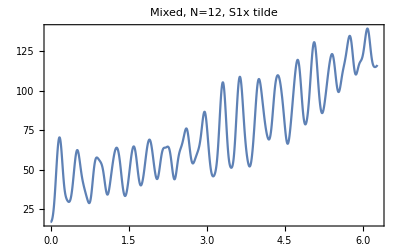

```mathematica
Plot[Re[fVar[s1$tilde$y,rho[t]]],{t,0,tmax},PlotLabel->"Mixed, N=12, S1x tilde"]
```